```mathematica
<<Units`
```

At the NASA website
  http://sunearth.gsfc.nasa.gov/eclipse/SEhelp/uncertainty2004.html
Fred Espenak gives the equations below.

He cites these references:
Huber, P. J., "Modeling the Length of Day and Extrapolating the Rotation of the Earth", Astronomical Amusements, Edited by F. Bonoli, S. De Meis, & A. Panaino, Rome, (2000).

Morrison, L. and Stephenson, F. R., "Historical Values of the Earth's Clock Error dT and the Calculation of Eclipses", J. Hist. Astron., Vol. 35 Part 3, August 2004, No. 120, pp 327-336 (2004).

Stephenson F.R and Houlden M.A., Atlas of Historical Eclipse Maps, Cambridge Univ.Press., Cambridge, 1986.

### Delta T from polynomial fits (Morrison and Stephenson [2004])

```mathematica
Clear[deltaTFitEqns,deltaTSubs,whichEqn,deltaTcorr]
deltaTFitEqns={
-0020.00-0000.000*u+32.000000*u^2,
10583.60-1014.410*u+33.783110*u^2-5.95205300*u^3-0.1798452000*u^4+0.0221741920*u^5+0.0090316521*u^6,
(01574.20-556.0100*u+71.234720*u^2+0.31978100*u^3-0.8503463000*u^4-0.0050509980*u^5+0.0083572073*u^6),
00120.00-0.980800*t-0.0153200*t^2+1/7129.00*t^3,
00008.83+0.160300*t-0.0059285*t^2+0.00013336*t^3-1/11740000.0*t^3,
00013.72-0.332447*t+0.0068612*t^2+0.00411160*t^3-0.0003743600*t^4+0.0000121272*t^5-0.0000001699*t^6+0.000000000875*t^7,
(00007.62+0.573700*t-0.2517540*t^2+0.01680668*t^3-0.0004473624*t^4+1/233174.00*t^5),
-0002.79+1.494119*t-0.0598939*t^2+0.00619660*t^3-0.0001970000*t^4,
00021.20+0.844930*t-0.0761000*t^2+0.00209360*t^3,
00029.07+0.407000*t-1/233.000*t^2+1/2547.000*t^3,
00045.45+1.067000*t-1/260.000*t^2-1/718.0000*t^3,
00063.86+0.334500*t-0.0603740*t^2+0.00172750*t^3+0.0006518140*t^4+0.000023735990*t^5,
00062.92+0.322170*t+0.0055890*t^2,-0020.00-0000.000*u+32.000000*u^2-0.5628*(2150-yr),
-0020.00-0000.000*u+32.000000*u^2};
deltaTSubs={
u->((yr-1820)/100),u->  (yr/100),
u->((yr-1000)/100),t->(yr-1600),
t->(yr-1700),t->(yr-1800),
t->(yr-1860),t->(yr-1900),
t->(yr-1920),t->(yr-1950),
t->(yr-1975),t->(yr-2000),
t->(yr-2000),u->((yr-1820)/100),u->((yr-1820)/100)};
whichEqn[yr_]:=Which[
               yr<-500,  1,-500≤yr<500,2,
  500≤yr<1600,  3,1600≤yr<1700,4,
1700≤yr<1800, 5,1800≤yr<1860,6,
1860≤yr<1900, 7,1900≤yr<1920,8,
1920≤yr<1941, 9,1941≤yr<1961,10,
1961≤yr<1986,11,1986≤yr<2005,12,
2005≤yr<2050,13,2050≤yr<2150,14,2150≤yr,15]
msDeltaTEqns = (Transpose[{deltaTFitEqns,deltaTSubs}]/.({eqn_,sub_}:>(eqn/.sub)));
msDeltaT[yr_]:=msDeltaTEqns[[whichEqn[yr]]]
deltaTcorr[yr_]:=(msDeltaT[yr]-0.000012932*(yr-1955)^2)/;(yr<1955 ∨yr>2005)
deltaTcorr[yr_]:=msDeltaT[yr]                                                               /;(1955<=yr<=2005)
```

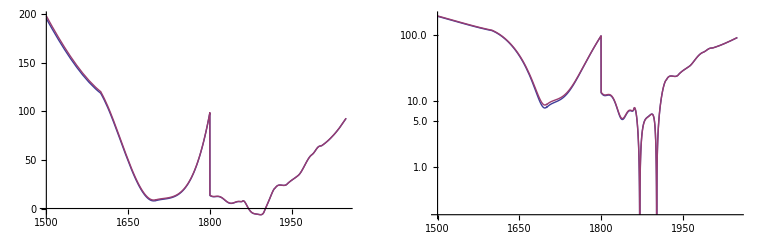

```mathematica
{
Plot[{deltaTcorr[yr], msDeltaT[yr]}, {yr,1500, 2050}, ImageSize->350],
LogPlot[{
Abs[deltaTcorr[yr]],
Abs[msDeltaT[yr]]}, {yr,1500, 2050}]}//GraphicsRow
```

```mathematica
{
Plot[{deltaTcorr[yr], msDeltaT[yr]}, {yr,1500, 2100}, ImageSize->350],
LogPlot[{
Abs[deltaTcorr[yr]],
Abs[msDeltaT[yr]]}, {yr,-4000, 5000}]}//GraphicsRow;
```

```mathematica
Table[{yr,msDeltaT[yr],
deltaTcorr[0],
deltaTcorr[msDeltaT[yr]],
whichEqn[yr],
deltaTcorr[msDeltaT[yr]],-0.000012932*(yr-1955)^2},{yr,1600, 2010,20}]//Transpose//MatrixForm;
```

```mathematica
Table[{yr,msDeltaT[yr],
whichEqn[yr],
deltaTcorr[msDeltaT[yr]],-0.000012932*(yr-1955)^2},{yr,1600, 2010,20}]//Transpose//MatrixForm
```

(1600 | 1620 | 1640 | 1660 | 1680 | 1700 | 1720 | 1740 | 1760 | 1780 | 1800 | 1820 | 1840 | 1860 | 1880 | 1900 | 1920 | 1940 | 1960 | 1980 | 2000
120. | 95.3782 | 65.2334 | 36.2988 | 15.3073 | 8.83 | 10.7308 | 14.286 | 25.8928 | 51.9483 | 13.72 | 11.8642 | 5.45572 | 7.62 | -5.00849 | -2.79 | 21.2 | 24.4074 | 33.1034 | 50.5148 | 63.86
4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 9 | 9 | 10 | 11 | 12
141569. | 153272. | 165754. | 179054. | 193214. | 208276. | 224285. | 241285. | 259325. | 278453. | 298716. | 320171. | 342870. | 366869. | 392226. | 419001. | 447255. | 477051. | 508454. | 541532. | 576354.
-1.62976 | -1.45129 | -1.28318 | -1.12541 | -0.977983 | -0.840903 | -0.71417 | -0.597782 | -0.491739 | -0.396042 | -0.310691 | -0.235686 | -0.171026 | -0.116711 | -0.0727425 | -0.0391193 | -0.0158417 | -0.0029097 | -0.0003233 | -0.0080825 | -0.0261873)

### Uncertainty Estimates from recent past

```mathematica
msFitUncy [y_]:=0.8 ((y-1820)/100)^2;
msDeltaTUncy = ({#,msFitUncy[#]}&/@Range[-1000,1200,100]);
shDeltaTUncy  = ({{1700, 5, 0.021}, {1800, 1, 0.004}, {1900, 0.1, 0.004}});
shEqnFitUncy =(a yr^2+b yr + c)/.FindFit[shDeltaTUncy[[All,{1,2}]],
a yr^2+b yr + c,{a,b,c},yr];
shFitUncy [y_]:=shEqnFitUncy/.yr->y
shFitUncy /@{1700,1800,1900};
```

### Huber estimate

```mathematica
FixStupidUnitsProblem[eqn_,u_]:=Simplify[eqn,Element[u, Reals]]/.{Abs[u]->u}
```

```mathematica
HuberUncyEst[y_,cal_,obslen_]:=((1/Second 365.25*n/Year*√(((n*q)/3)*(1+n/m)))//.
{n->Abs[(y-cal)]Year,
m->obslen Year,
q->58/1000 (Second/1000 )^2/Year,
Year->Convert[1 Year, 1 Second]})//FixStupidUnitsProblem[#,Second]&
HuberUncyEst[y_,-500,2500];
```

```mathematica
huDeltaT=Flatten[{
{#,HuberUncy Est[#,-500,2500]}&/@Range[-4000,-500,100], 
{#,HuberUncy Est[#,2005,2500]}&/@Range[2005,5000,100] 
},1];
( huDeltaT/. {y_,s_}:>{y,s,360/(24*60*60) s})//Transpose//MatrixForm;
```

### Combined Data

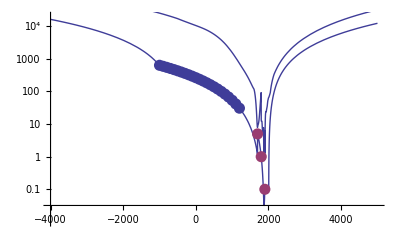

```mathematica
Clear[deltaTUncy]
deltaTUncy[y_]:=HuberUncyEst[y,-500,2500]/;(-4000≤y<-1000)
deltaTUncy[y_]:=msFitUncy[y]/;(-1000≤y<1700)
deltaTUncy[y_]:=shFitUncy[y]/;(1700≤y<1900)
deltaTUncy[y_]:=0.1/;(1900≤y<2005)
deltaTUncy[y_]:=HuberUncyEst[y,2005,2500]/;(2005≤y≤5000)
Show[{
LogPlot[deltaTUncy[x],{x,-4000,5000}],
LogPlot[Abs[deltaTcorr[yr]], {yr,-4000, 5000}],
ListLogPlot[{msDeltaTUncy,(#/.{y_,s_,l_}:>{y,s})&/@shDeltaTUncy},PlotStyle->PointSize[0.02]]
},{PlotRange->{{-4000,5000},{0.01//Log,20000//Log}}}]
```

### Export Data

```mathematica
deltaTTable = Table[{yr,deltaTcorr[yr]//N[#]& ,deltaTUncy[yr]//N[#,19]& },{yr,-4000,5000,1}];
Export["astronomy-dynamicaltime-terrestrialtime.csv",deltaTTable, "CSV"];
```